Syntax::stresc: Unknown string escape \M.

The 3PL model was selected.

Test Statistics

(N of Items | 15
Sample Size | 500
Mean | 9.664
SE of Mean | 0.119074
SD | 2.66257
Skewness | -0.411622
Kurtosis | 2.55284
Min | 2
Max | 15)

Item Statistics

(Item | Number of Respondents | Correct Response Rate | Item Threshold | Item-Total Correlation
Item01 | 500 | 0.746 | -0.661955 | 0.374648
Item02 | 500 | 0.754 | -0.687131 | 0.393205
Item03 | 500 | 0.726 | -0.60076 | 0.3213
Item04 | 500 | 0.776 | -0.758754 | 0.502824
Item05 | 500 | 0.804 | -0.855996 | 0.329054
Item06 | 500 | 0.864 | -1.09847 | 0.37686
Item07 | 500 | 0.716 | -0.570999 | 0.483067
Item08 | 500 | 0.588 | -0.222403 | 0.405215
Item09 | 500 | 0.364 | 0.347787 | 0.22482
Item10 | 500 | 0.662 | -0.417928 | 0.314446
Item11 | 500 | 0.286 | 0.565108 | 0.455081
Item12 | 500 | 0.274 | 0.60076 | 0.467784
Item13 | 500 | 0.634 | -0.342466 | 0.47125
Item14 | 500 | 0.764 | -0.719229 | 0.484841
Item15 | 500 | 0.706 | -0.541737 | 0.412775)

Section 4.5 Item Parameter Estimation: The computation may take some time when there are many items.

(Item | Slope | Location | Lower Asymptote | PSD(Slope) | PSD(Loc) | PSD(LA)
Item01 | 0.817585 | -0.833699 | 0.280362 | 0.181931 | 0.62788 | 0.170187
Item02 | 0.859864 | -1.11942 | 0.185206 | 0.156605 | 0.471175 | 0.148788
Item03 | 0.657401 | -0.698975 | 0.304841 | 0.161984 | 0.797501 | 0.172825
Item04 | 1.55014 | -0.948784 | 0.144197 | 0.227304 | 0.215632 | 0.104374
Item05 | 0.721491 | -1.55837 | 0.258387 | 0.147605 | 0.699878 | 0.186009
Item06 | 1.02165 | -1.87593 | 0.182696 | 0.17138 | 0.422984 | 0.157669
Item07 | 1.25518 | -0.655375 | 0.179313 | 0.214443 | 0.289333 | 0.116538
Item08 | 0.748492 | -0.154612 | 0.130774 | 0.147744 | 0.394311 | 0.107746
Item09 | 1.17749 | 2.28703 | 0.292968 | 0.492754 | 0.422869 | 0.0440459
Item10 | 0.546446 | -0.505195 | 0.222122 | 0.131173 | 0.778513 | 0.156163
Item11 | 1.47599 | 1.08971 | 0.062748 | 0.263346 | 0.120313 | 0.0320583
Item12 | 1.47844 | 1.08493 | 0.0462087 | 0.245315 | 0.115012 | 0.0276025
Item13 | 0.897851 | -0.501889 | 0.0959918 | 0.142236 | 0.271516 | 0.0857765
Item14 | 1.41806 | -0.787882 | 0.225956 | 0.247707 | 0.291208 | 0.125219
Item15 | 0.907561 | -0.812479 | 0.153152 | 0.158805 | 0.383328 | 0.125407)

Section 4.2 Item Response Function

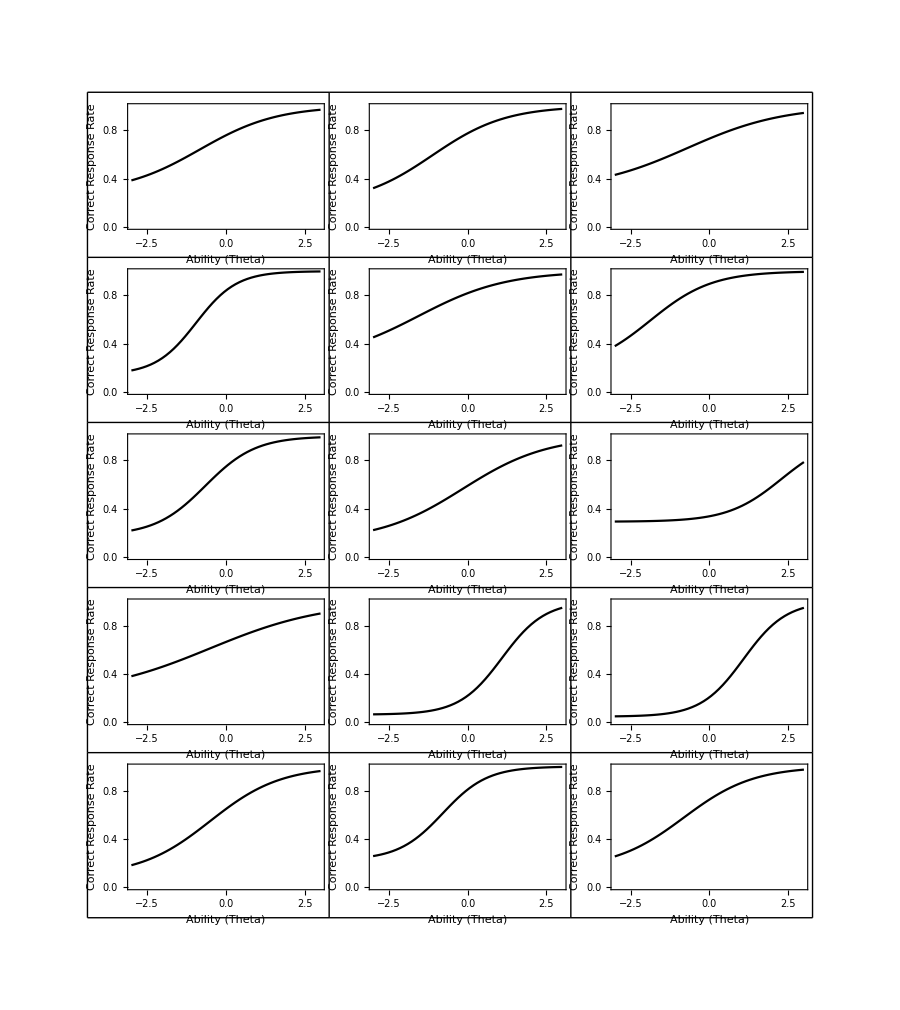

Section 4.2.5 Test Response Function

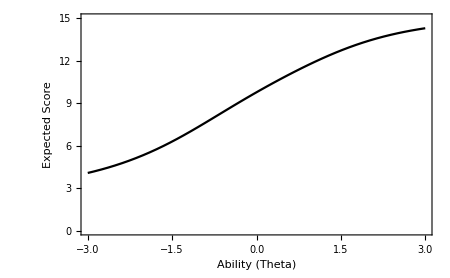

Section 4.4 Item Information Function

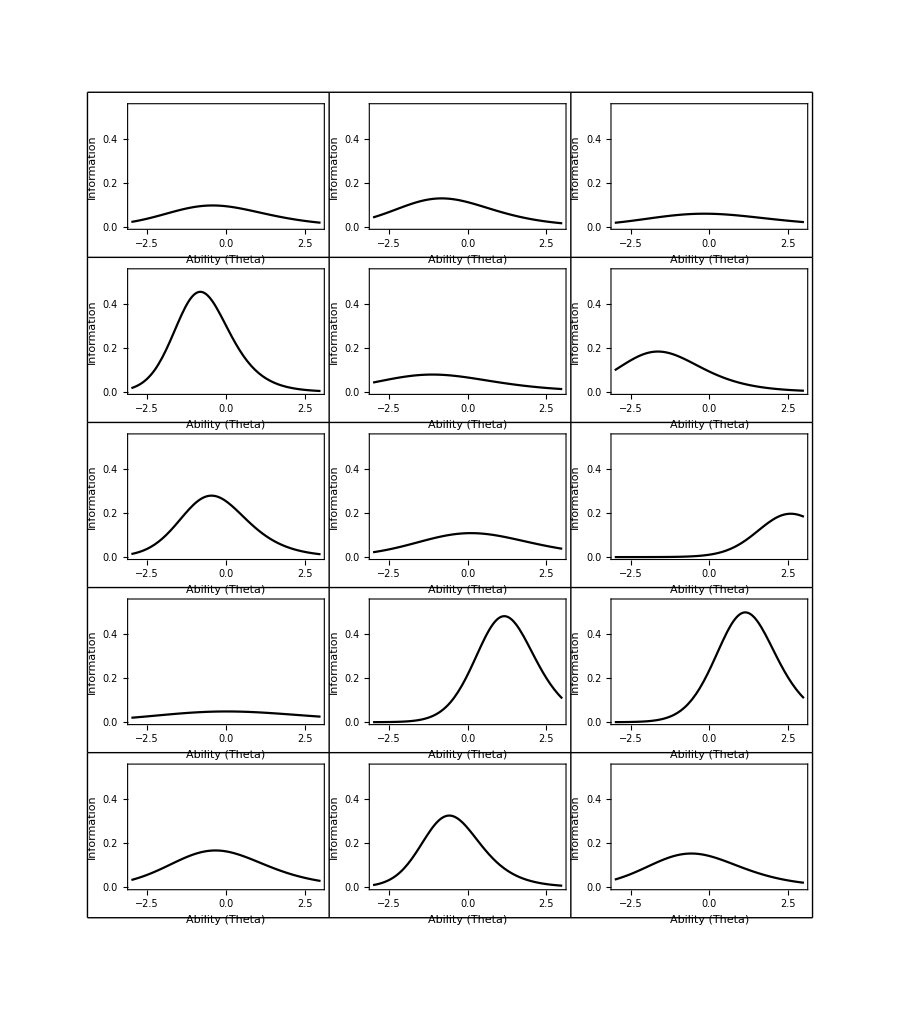

Section 4.4.1 Test Information Function

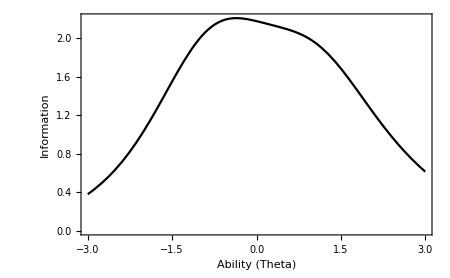

Section 4.3 Ability Parameter Estimation: The results are recoreded in the Excel output file.

Section 4.6 Model Fit

NotebookEvaluate::nbnfnd: Unable to find the notebook /Users/napier3/Dropbox/Git/Exametrika/tests/testthat/mtmk_v13/mod\Module_Modelfit.nb.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 1 of {} does not exist.

Set::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

testfitout

itemfitout

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Join::heads: Heads List and Transpose at positions 1 and 4 are expected to be the same.

```mathematica
(*----------------------------------------------------*)
(*       Shojima, K. (30/04/2022)                         *)
(*          Item response theory on Mathematica.           *)
(*          http://shojima.starfree.jp/tde/               *)
(*----------------------------------------------------*)

(*DATA SPECIFICATION*)

(*Specify the file name of your data.*)
datafile="J15S500.csv";
(*Put the data file in the same folder where this Mathematica program is placed.*)
(*Do not delete the folder named as "mod."*)

(*Specify the row number in which the item labels are input. The program considers the reponse data start from the next row.*)
itemlabelrow=1;

(*Specify the column number in which the student IDs are input. The program considers the reponse data start from the next column.*)
studentIDcolumn=1;

(*The missing indicator must be a numerical value.*)
mi=-99;

(*----------------------------------------------------*)
(*ANALYSIS SETTING*)

(*Select 2-, 3-, or 4-parameter logistic model.*)
model=3;

(*Position the cursor anywhere in the program commands and hit [shift+enter], and the program runs.*)
(*----------------------------------------------------*)
dir=NotebookDirectory[];
NotebookEvaluate[dir<>"mod/Module_IRT.nb"];
irt[data];
(*----------------------------------------------------*)
```